# Autocorrelation functions

## Loading files

```mathematica
Needs["ErrorBarPlots`"]
```

#### Load trajectories

```mathematica
listoftrajs=ReadList[NotebookDirectory[]<>"data/mov150616num1b_listoftrajectories.dat"];
```

## Processing trajectories

```mathematica
Magnify[HighlightImage[Import[NotebookDirectory[]<>"data/mov150616num1b_smoothed.png"],Graphics[{Directive[RandomColor[],Thickness[0.002],Opacity[0.8]],#}&/@(Line/@listoftrajs)]],0.5]
```

-Graphics-

### full statistics

#### calculating the statistics

```mathematica
listofdrs=Differences/@listoftrajs;
```

```mathematica
listofnormalizeddrs=Normalize/@#&/@listofdrs;
```

```mathematica
listofangles=MapThread[ArcTan,#//Transpose]&/@listofnormalizeddrs;
```

```mathematica
listofangledeltas=Table[listofangles[[i]]-listofangles[[i,1]],{i,Length@listofangles}];
```

```mathematica
cosdecay=Cos/@#&/@listofangledeltas;
cos2decay=Cos/@#&/@(2*listofangledeltas);
```

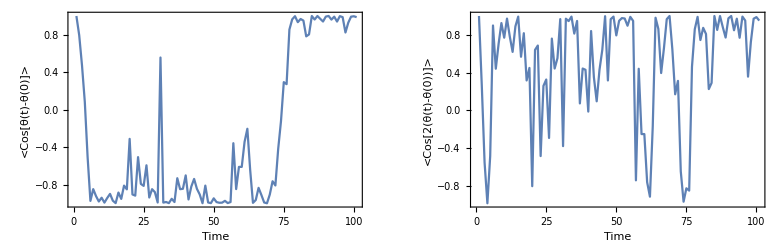

```mathematica
GraphicsRow[{ListLinePlot[cosdecay[[12]],Frame->True,ImageSize->Medium,FrameLabel->{Style["Time",14],Style["<Cos[θ(t)-θ(0)]>",14]}],ListLinePlot[cos2decay[[12]],Frame->True,ImageSize->Medium,FrameLabel->{Style["Time",14],Style["<Cos[2(θ(t)-θ(0))]>",14]}]}]
```

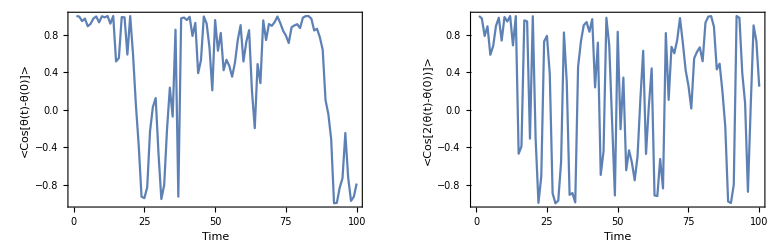

```mathematica
GraphicsRow[{ListLinePlot[cosdecay[[16]],Frame->True,ImageSize->Medium,FrameLabel->{Style["Time",14],Style["<Cos[θ(t)-θ(0)]>",14]}],ListLinePlot[cos2decay[[16]],Frame->True,ImageSize->Medium,FrameLabel->{Style["Time",14],Style["<Cos[2(θ(t)-θ(0))]>",14]}]}]
```

```mathematica
norm=Table[0,{i,Max@(Length/@cosdecay)}];
Table[Table[norm[[i]]++;,{i,Length@cosdecay[[j]]}],{j,Length@cosdecay}];
```

```mathematica
autocorr1=Table[0,{i,Max@(Length/@cosdecay)}];
Table[Table[autocorr1[[i]]+=cosdecay[[j,i]],{i,Length@cosdecay[[j]]}],{j,1,Length@cosdecay}];
autocorr2=Table[0,{i,Max@(Length/@cos2decay)}];
Table[Table[autocorr2[[i]]+=cos2decay[[j,i]],{i,Length@cos2decay[[j]]}],{j,1,Length@cos2decay}];
```

```mathematica
norm
```

{39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,35,35,35,35,35,35,34,34,34,33,33,33,32,31,31,31,31,31,31,31,31,30,30,29,29,29,29,28,28,27,26,26,26,25,24,24,23,22,22,21,20,19,19,18,17,16,16,16,16,16,15,15,14,14,14,14,13,13,13,13,12,9,2}

```mathematica
var1=Table[{},{i,Max@(Length/@cosdecay)}];
Table[Table[AppendTo[var1[[i]],cosdecay[[j,i]]],{i,Length@cosdecay[[j]]}],{j,1,Length@cosdecay}];
error1=(Sqrt/@Variance/@var1/(Sqrt/@norm));
 var2=Table[{},{i,Max@(Length/@cos2decay)}];
Table[Table[AppendTo[var2[[i]],cos2decay[[j,i]]],{i,Length@cos2decay[[j]]}],{j,1,Length@cos2decay}];
error2=(Sqrt/@Variance/@var2/(Sqrt/@norm));
```

```mathematica
edata1=Thread[{Thread[{Range[0,Length@autocorr1-1]*frametime,(autocorr1/norm)}],(ErrorBar/@error1)}];
edata2=Thread[{Thread[{Range[0,Length@autocorr2-1]*frametime,(autocorr2/norm)}],(ErrorBar/@error2)}];
```

#### Plotting the statistics

```mathematica
frametime=0.5;
data1={Range[0,Length@autocorr1-1]*frametime,(autocorr1/norm)}//Thread;
data2={Range[0,Length@autocorr1-1]*frametime,(autocorr2/norm)}//Thread;
(*ListPlot[{data1,data2},Joined->True,PlotMarkers->Automatic,Frame->True,GridLines->Automatic,PlotLegends->{Style["<Cos[θ(t)-θ(0)]>",14],Style["<Cos[2(θ(t)-θ(0))]>",14]},FrameLabel->{Style["Time",14]},PlotLabel->Style["Autocorrelation functions",14]]*)
```

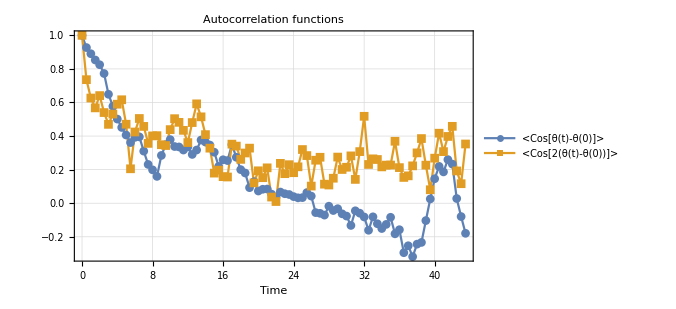

```mathematica
endframe=88;
ListPlot[{data1[[;;endframe]],data2[[;;endframe]]},Joined->True,PlotMarkers->Automatic,Frame->True,GridLines->Automatic,PlotLegends->{Style["<Cos[θ(t)-θ(0)]>",14],Style["<Cos[2(θ(t)-θ(0))]>",14]},FrameLabel->{Style["Time",14]},PlotLabel->Style["Autocorrelation functions",14],ImageSize->500]
```

#### fitting it

```mathematica
nlm1=FindFit[data1,Exp[-s/b],{b},s]
nlm2=FindFit[data2,(1-c)Exp[-s/b]+c,{b,c},s]
```

{b→7.89369}

{b→3.96005,c→0.262099}

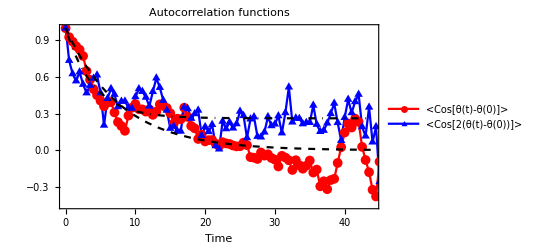

```mathematica
Show[{ListPlot[{data1,data2},Joined->True,PlotStyle->{{Red},{Blue}},PlotMarkers->{{●,10},{▲,10}},PlotRange->{{0,44},Automatic},PlotLegends->Placed[{Style["<Cos[θ(t)-θ(0)]>",12],Style["<Cos[2(θ(t)-θ(0))]>",12]},{0.78,0.85}],FrameLabel->{Style["Time",14]},PlotLabel->Style["Autocorrelation functions",14]],Plot[{Evaluate[Exp[-s/b]/.nlm1],Evaluate[(1-c)Exp[-s/b]+c/.nlm2]},{s,0,44},PlotStyle->{{Black,Dashed},{Black,DotDashed}},PlotRange->All]},Frame->True]
```

```mathematica
Show[{ErrorListPlot[{edata1,edata2},PlotMarkers->{{●,10},{▲,10}},PlotStyle->{Directive[Red,Thickness[0.001]],Directive[Blue,Thickness[0.001]]},PlotRange->{{0,44},Automatic},Joined->True,PlotLegends->Placed[{Style["<Cos[θ(t)-θ(0)]>",12],Style["<Cos[2(θ(t)-θ(0))]>",12]},{0.78,0.85}],FrameLabel->{Style["Time",14]},PlotLabel->Style["Autocorrelation functions",14]],Plot[{Evaluate[Exp[-s/b]/.nlm1],Evaluate[(1-c)Exp[-s/b]+c/.nlm2]},{s,0,44},PlotStyle->{{Black,Dashed},{Black,DotDashed}},PlotRange->All]},Frame->True]
```

-Graphics-